```mathematica
SetOptions[EvaluationNotebook[],Background->ColorData["Legacy","Smoke"]]
```

```mathematica
(* functions to support data extraction, reporting, and plotting *)
readData[validDataPath_]:=Module[{fpath=validDataPath},Association[Import[fpath,"JSON"]]];
extractData[experiment_]:=Module[{expmt=experiment},{expmt["domain"],DeleteDuplicates[Map[Association,expmt["population"]]]}]
reportPopulation[population_]:=Module[{pop=population,census,scores,sum,max,min},
census=Length[pop];
scores=Map[#["score"]&, pop];
sum=Fold[Plus, 0, scores];
max=Max[scores];
min=Min[scores];
Print[StringTemplate["`a` unique pop members with:"][<|"a"->census|>]];
Print[StringTemplate["  max `a`"][<|"a"->max|>]];
Print[StringTemplate["  avg `a`"][<|"a"->sum/census|>]];
Print[StringTemplate["  ctr `a`"][<|"a"->(min+max)/2|>]];
Print[StringTemplate["  min `a`"][<|"a"->min|>]]
]

(* extract all the data *)
filenameFromParts[root_,exp_,gen_]:=Module[{r=root,e=exp,g=gen,f},
f=StringTemplate["`a`-`b`.json"][<|"a"->e,"b"->g|>];
FileNameJoin[{r,e,f}]
]
unpackExperiment[experimentJSON_,gen_]:=Module[{expmtFile=experimentJSON,g=gen,cityMap,pops,scores,routes},
{cityMap,pops}=extractData[readData[expmtFile]];
scores=Map[#["score"]&,pops];
routes=Map[#["route"]&,pops];
{g,cityMap,routes,scores}
]
extractFullExperiment[rootDataFolder_,experimentStamp_,targetGenerations_]:=
Module[{dataFolder=rootDataFolder,expmtStamp=experimentStamp,gens=targetGenerations,rawRun,cookedRun},
rawRun=Map[unpackExperiment[filenameFromParts[dataFolder,expmtStamp,#],#]&,gens];
cityMap=First[rawRun][[2]];
cookedRun= Map[{#[[1]],<|routes->#[[3]],scores->#[[4]],max->Max[#[[4]]],min->Min[#[[4]]],mean->Plus[#[[4]]]/Length[#[[4]]]|>}&,rawRun]
]

plotBestRoute[cityPositions_,population_]:=Module[{cities=cityPositions, pop=population},
ListLinePlot[Map[cities[[#+1]]&,First[pop]["route"]],AspectRatio->1]
]
travSalesPlot[validDataPath_]:=Module[{fname=validDataPath},
{cityXYs,pops}=extractData[readData[fname]];
plotBestRoute[cityXYs,pops]
]
```

```mathematica
(* these need to be set up per run *)
rootDataFolder=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data"}];
experimentFolder="20230217182025Z";
minGen=1;
maxGen=999;
```

```mathematica
gen=1;
filenameFromParts[rootDataFolder,experimentFolder,gen];
unpackExperiment[%,gen]
```

{1,x[domain],x[Association[population][route]],x[Association[population][score]]}

```mathematica
fullExpmt=extractFullExperiment[rootDataFolder,experimentFolder,Range[1,999]]
fullExpmtDS=Dataset[%];
[#][max]&/@fullExpmt
```

```mathematica
3
```

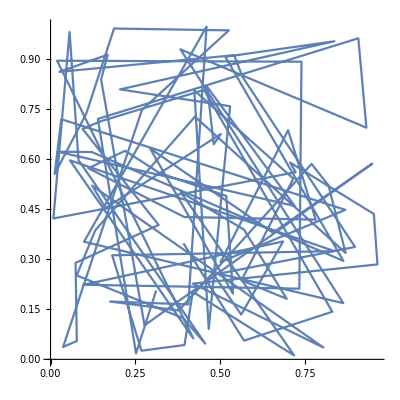

```mathematica
travSalesPlot["~/projects/elixir/gelid/gelid/data/20230217182025Z-1.json"]
```

```mathematica
readData["~/projects/elixir/gelid/gelid/data/20230217182025Z-1.json"];
{cityPositions,population}=extractData[%];
cityPositions;
population;
plotBestRoute[cityPositions,population]
```

-Graphics-

```mathematica
$UserDocumentsDirectory
$WolframDocumentsDirectory
$InitialDirectory
$BaseDirectory
Directory[]
NotebookDirectory[]
```

/Users/bradheintz/Documents

/Users/bradheintz/Documents/Wolfram

/Users/bradheintz

/Library/Mathematica

/Users/bradheintz

/Users/bradheintz/projects/elixir/gelid/gelid/scripts/